# Discontinuous Galerkin

## Weak Formulation (Modal DG)

By Manuel A. Diaz, NTU, 2012.07.10

```mathematica
Quit[]; (* to reset Mathematica kernel *)
```

## Legendre Polynomials

```mathematica
legendreP =Table[LegendreP[i,𝒳],{i,0,6}];
Column[legendreP] // TraditionalForm
```

1
𝒳
1/2 (3 𝒳^2-1)
1/2 (5 𝒳^3-3 𝒳)
1/8 (35 𝒳^4-30 𝒳^2+3)
1/8 (63 𝒳^5-70 𝒳^3+15 𝒳)
1/16 (231 𝒳^6-315 𝒳^4+105 𝒳^2-5)

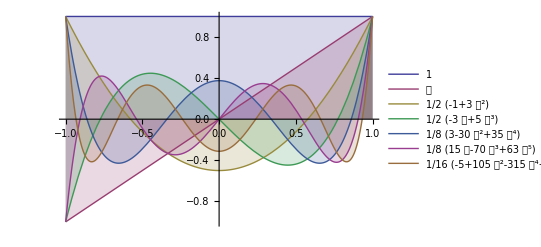

```mathematica
Plot[Evaluate[legendreP],{𝒳,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

## Scaled Orthogonal Polynomials

Define the size of our interval, I_j, as Δx_j. This interval and it will be identified by its middel point x_j. Notice that our basis polynomials work on the range of [-1,1]. Thus we are now interested in finding a way to scale them for interval I_j with range [-Δx/2,Δ/2].

The first idea to scale them is by making the change of variable 𝒳 → x-x_j, and using grand Schmidt ortogonalization process to build a new set or orthogonal polynomials.

### Initialize Notation

```mathematica
Needs["Notation`"]
```

based on http://en.wikipedia.org/wiki/Gram-Schmidt_process, we configure:

```mathematica
Notation[<a_[x_],b_[x_]> ⟹ Integrate[a_[x_] b_[x_],{x_,-Subscript[Δx, j]/2,Subscript[Δx, j]/2}]]
Notation[<a_,b_> ⟹ Integrate[a_ b_,{z,-Subscript[Δx, j]/2,Subscript[Δx, j]/2}]]
```

```mathematica
Notation[Subscript[proj, u_][v_] ⟹ (<u_,v_>)/(<u_,u_>)u_]
```

Testing:

```mathematica
<Subscript[v, 1][z],Subscript[v, 1][z]>
```

∫_(-Δx_j/2)^(Δx_j/2) v_1[z]^2 ⅆz

```mathematica
<a z,z>
```

(a Δx_j^3)/12

```mathematica
(<a[z],b[z]>)/(<a[z],a[z]>)a[z] == Subscript[proj, a[z]][b[z]]
```

True

```mathematica
Symbolize[Subscript[Δx, j]]; Symbolize[Subscript[x, j]];Symbolize[Subscript[I, j]];
```

### Building Scaled Legendre Polynomials using Gram Schmidt Orthogonalization process

#### Procedure 1: (not so good...)

based on http : // en.wikipedia.org/wiki/Gram - Schmidt_process, we configure :

Defining our initial vectors,

```mathematica
Table[Subscript[v, i]=z^i,{i,0,6}](* here z = x-Subscript[x, j] *)
```

{1,z,z^2,z^3,z^4,z^5,z^6}

Compute initial projection

```mathematica
Subscript[u, 0]=Subscript[v, 0]
```

1

```mathematica
Subscript[u, 1]=Subscript[v, 1]-Subscript[proj, Subscript[u, 0]][Subscript[v, 1]]
```

z

```mathematica
scaledLegendre = Table[Subscript[u, i+1]=Subscript[v, i+1]-Subscript[proj, Subscript[u, i-1]][Subscript[v, i+1]] -Subscript[proj, Subscript[u, i]][Subscript[v, i+1]],{i,1,5}] ;
```

```mathematica
scaledLegendre /. z -> x-Subscript[x, j]//Column
```

(x-x_j)^2-Δx_j^2/12
(x-x_j)^3-3/20 (x-x_j) Δx_j^2
(x-x_j)^4-3/14 Δx_j^2 ((x-x_j)^2-Δx_j^2/12)
(x-x_j)^5-5/18 Δx_j^2 ((x-x_j)^3-3/20 (x-x_j) Δx_j^2)
(x-x_j)^6-(885 Δx_j^2 ((x-x_j)^4-3/14 Δx_j^2 ((x-x_j)^2-Δx_j^2/12)))/4444

#### Procedure 2: (way much better)

based on http : // mathworld.wolfram.com/Gram - SchmidtOrthonormalization.html, we configure :

```mathematica
Subscript[p, 0]=1;
Subscript[p, 1]=(z - (<z Subscript[p, 0],Subscript[p, 0]>)/(<Subscript[p, 0],Subscript[p, 0]>))Subscript[p, 0];
```

```mathematica
scaledLegendre=Table[Subscript[p, i+1]=(z - (<z Subscript[p, i],Subscript[p, i]>)/(<Subscript[p, i],Subscript[p, i]>))Subscript[p, i] -(<Subscript[p, i],Subscript[p, i]>)/(<Subscript[p, i-1],Subscript[p, i-1]>)Subscript[p, i-1] ,{i,1,6}]//Expand ;
```

```mathematica
scaledLegendre = Join[{Subscript[p, 0],Subscript[p, 1]},scaledLegendre];
```

```mathematica
scaledLegendre /.z-> x-Subscript[x, j]//Column
```

1
x-x_j
(x-x_j)^2-Δx_j^2/12
(x-x_j)^3-3/20 (x-x_j) Δx_j^2
(x-x_j)^4-3/14 (x-x_j)^2 Δx_j^2+(3 Δx_j^4)/560
(x-x_j)^5-5/18 (x-x_j)^3 Δx_j^2+5/336 (x-x_j) Δx_j^4
(x-x_j)^6-15/44 (x-x_j)^4 Δx_j^2+5/176 (x-x_j)^2 Δx_j^4-(5 Δx_j^6)/14784
(x-x_j)^7-21/52 (x-x_j)^5 Δx_j^2+(105 (x-x_j)^3 Δx_j^4)/2288-(35 (x-x_j) Δx_j^6)/27456

How about using rewritting in the form(x-x_j)/Δx_j. Lets explore this form...

```mathematica
scaledLegendre2 =Divide[scaledLegendre,{1,Subscript[Δx, j],Subscript[Δx, j]^2,Subscript[Δx, j]^3,Subscript[Δx, j]^4,Subscript[Δx, j]^5,Subscript[Δx, j]^6,Subscript[Δx, j]^7}]//Expand;
scaledLegendre2/.z->x-Subscript[x, j]//Column
```

1
(x-x_j)/Δx_j
-1/12+(x-x_j)^2/Δx_j^2
(x-x_j)^3/Δx_j^3-(3 (x-x_j))/(20 Δx_j)
3/560+(x-x_j)^4/Δx_j^4-(3 (x-x_j)^2)/(14 Δx_j^2)
(x-x_j)^5/Δx_j^5-(5 (x-x_j)^3)/(18 Δx_j^3)+(5 (x-x_j))/(336 Δx_j)
-5/14784+(x-x_j)^6/Δx_j^6-(15 (x-x_j)^4)/(44 Δx_j^4)+(5 (x-x_j)^2)/(176 Δx_j^2)
(x-x_j)^7/Δx_j^7-(21 (x-x_j)^5)/(52 Δx_j^5)+(105 (x-x_j)^3)/(2288 Δx_j^3)-(35 (x-x_j))/(27456 Δx_j)

#### Procedure 3: (the mathematica way)

```mathematica
scaledLegendre3 = Orthogonalize[{1,z,z^2,z^3,z^4,z^5,z^6},Integrate[#1 #2,{z,-1,1}]&] //Expand;
```

```mathematica
scaledLegendre3 /.z->2(x-Subscript[x, j])/Subscript[Δx, j] //Column
```

1/(√2)
(√6 (x-x_j))/Δx_j
-(√(5/2))/2+(3 √10 (x-x_j)^2)/Δx_j^2
(10 √14 (x-x_j)^3)/Δx_j^3-(3 √(7/2) (x-x_j))/Δx_j
9/(8 √2)+(105 √2 (x-x_j)^4)/Δx_j^4-(45 (x-x_j)^2)/(√2 Δx_j^2)
(126 √22 (x-x_j)^5)/Δx_j^5-(35 √22 (x-x_j)^3)/Δx_j^3+(15 √(11/2) (x-x_j))/(4 Δx_j)
-(5 √(13/2))/16+(462 √26 (x-x_j)^6)/Δx_j^6-(315 √(13/2) (x-x_j)^4)/Δx_j^4+(105 √(13/2) (x-x_j)^2)/(4 Δx_j^2)

Their orthogonal behavior:

Here, I need to re-define in this case my notation becuase here the integration is obver the classical range of [-1,1]

```mathematica
Notation[<a_,b_> ⟹ Integrate[a_ b_,{z,-1,1}]]
```

```mathematica
Table[(<scaledLegendre3[[i]],scaledLegendre3[[j]]>),{i,1,7},{j,1,7}] //MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)

Therefore this are normalized and scaled legrendre polynomials!

### Normalization Constants

```mathematica
coefficients = Table[(<Subscript[p, n],Subscript[p, m]>),{n,0,7},{m,0,7}];
```

```mathematica
coefficients // TableForm
```

1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/324 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/43740 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/6123600 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/868020300 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/123744973968 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/17695531277424 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2535155705459520

```mathematica
coef = Diagonal[coefficients]; Table[Subscript[a, i]=coef[[i+1]],{i,0,7}]
```

{1/3,1/324,1/43740,1/6123600,1/868020300,1/123744973968,1/17695531277424,1/2535155705459520}

#### Derivative of the scaled polynomials

```mathematica
dscaledpolynomials = D[scaledLegendre,z];
dscaledpolynomials /.z -> x-Subscript[x, j] //Column
```

0
1
2 (-1/6+x)
-1/60+3 (-1/6+x)^2
1/21 (1/6-x)+4 (-1/6+x)^3
5/27216-5/54 (-1/6+x)^2+5 (-1/6+x)^4
(5 (-1/6+x))/7128-5/33 (-1/6+x)^3+6 (-1/6+x)^5
-35/20015424+(35 (-1/6+x)^2)/20592-35/156 (-1/6+x)^4+7 (-1/6+x)^6

```mathematica
Table[Subscript[dp, i]= dscaledpolynomials[[i+1]],{i,0,7}];
```

```mathematica
dcoefficients = Table[Subscript[b, n,m]= (<Subscript[p, n],Subscript[dp, m]>),{n,0,7},{m,0,7}];
```

```mathematica
dcoefficients //TableForm
```

0 | 1/3 | 0 | 1/270 | 0 | 1/30618 | 0 | 1/3752892
0 | 0 | 1/162 | 0 | 1/17010 | 0 | 1/2020788 | 0
0 | 0 | 0 | 1/14580 | 0 | 1/1653372 | 0 | 1/202656168
0 | 0 | 0 | 0 | 1/1530900 | 0 | 1/181870920 | 0
0 | 0 | 0 | 0 | 0 | 1/173604060 | 0 | 1/21278897640
0 | 0 | 0 | 0 | 0 | 0 | 1/20624162328 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2527933039632
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

### Plot Scaled Legendre Polynomials

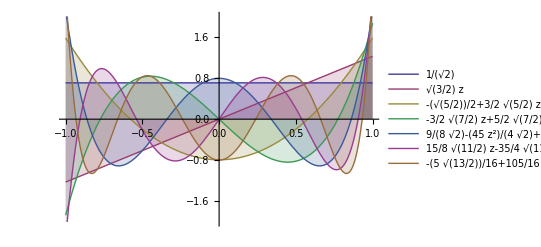

```mathematica
orthogonalpolinomials = scaledLegendre3 /. Subscript[Δx, j]->1;
Plot[Evaluate[orthogonalpolinomials],{z,-1,1},
Filling->Axis,PlotLegends->"Expressions",PlotRange->{-2,2}]
```

So having this scaled functions we can think on using them as basis functions to expand otherpolynomials just as we did in FEM,

## Basis Function for 1D cases:

Here we are interested in understanding the expansion of these polynomials from a continuous form to a pieze wize for of the from:

```mathematica
Quit[]; (* to reset Mathematica kernel *)
```

From previous calculations we can do:

```mathematica
Table[Subscript[v, i]= Expand[Subscript[p, i]],{i,0,6}];(* recall that z -> x-Subscript[x, j] *)
```

```mathematica
Table[Subscript[v, i],{i,0,6}]//MatrixForm
```

(1
z
z^2-Δx_j^2/12
z^3-(3 z Δx_j^2)/20
z^4-3/14 z^2 Δx_j^2+(3 Δx_j^4)/560
z^5-5/18 z^3 Δx_j^2+(5 z Δx_j^4)/336
z^6-15/44 z^4 Δx_j^2+5/176 z^2 Δx_j^4-(5 Δx_j^6)/14784)

Now assume that we are interested in using these polynomials with Gauss-Lobatto-Legendre for 4 points scaled to fit in I_j, the corresponding local coordiantes of the abscissas and weight are:

```mathematica
{Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3],Subscript[ξ, 4]} = {-1/2,-(√5)/10,(√5)/10,1/2}; {Subscript[w, 1],Subscript[w, 2],Subscript[w, 3],Subscript[w, 4]}={1/12,5/12,5/12,1/12};
```

As an example, here I’ll assume and a random interval with left and right boundaries located at [1/3,2/3]. First we proceed to create the corresponding local nodes inside the cell:

```mathematica
Subscript[x, l] = 1/3; Subscript[x, r] =2/3; Subscript[Δx, j]=Subscript[x, r]-Subscript[x, l];Subscript[x, j] = Subscript[Δx, j]/2; {Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4]} =Subscript[x, j]+{Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3],Subscript[ξ, 4]} Subscript[Δx, j]
```

{0,1/6-1/(6 √5),1/6+1/(6 √5),1/3}

notice that the Global coordinates will be given by,

```mathematica
X= Subscript[x, l]+{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4]}
```

{1/3,1/2-1/(6 √5),1/2+1/(6 √5),2/3}

Evaluating every escaled polynomial for the computed abcisas we get:

```mathematica
vandermonde = Table[Subscript[v, i]/.z->Subscript[x, l],{l,1,4},{i,0,3}];
vandermonde //MatrixForm
```

(1 | 0 | -1/108 | 0
1 | 1/6-1/(6 √5) | -1/108+(1/6-1/(6 √5))^2 | (1/6-1/(6 √5))^3+1/60 (-1/6+1/(6 √5))
1 | 1/6+1/(6 √5) | -1/108+(1/6+1/(6 √5))^2 | 1/60 (-1/6-1/(6 √5))+(1/6+1/(6 √5))^3
1 | 1/3 | 11/108 | 17/540)

if for the case every we are using equally distributed cells, we can just program the numerical version of this matrix:

```mathematica
vandermonde //MatrixForm//N
```

(1. | 0. | -0.0833333 | 0.
1. | 0.276393 | -0.00694013 | -0.0203444
1. | 0.723607 | 0.440273 | 0.270344
1. | 1. | 0.916667 | 0.85)

### Initialization

```mathematica
Symbolize[Subscript[u, h]];Symbolize[u^_];
```

```mathematica
Subscript[u, 1]//InputForm
```

Subscript[u, 1]

```mathematica
u^(l) // InputForm
```

u⎵Superscript⎵LeftParenthesis⎵l⎵RightParenthesis

```mathematica
Table[ToExpression[RowBox[{"{",ToString[i],"}"}]],{i,10}]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}

```mathematica
Notation[∫_Subscript[I, j] f_ⅆx_ ⟹ Integrate[f_,{x_,-Subscript[Δx, j]/2,Subscript[Δx, j]/2}]]
```

### Degrees of Freedom u_j^(l)

For u_j element using the continuous function u(x,t). If we define the degrees of freedom as:

u_j^(l) = u_j^(l)[t] = 1/Δx_j^(l+1)∫_I_j u[x,t] v_l^(j)[x]ⅆx, for l = 1,...,k

of course, we need to define u[x,t] in order to continue. We traditionally have two choises a continuous or a discontinuous function,

#### Case1: assume the Riemann IC:

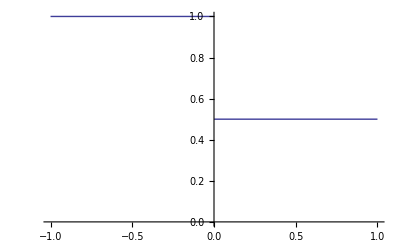

```mathematica
u[x_,t_]:= Piecewise[{{1,x<0},{0.5,x>=0}}];
Plot[u[x,t],{x,-1,1},PlotRange->{0,1}]
```

#### Case2: assume Sinusoidal wave function :

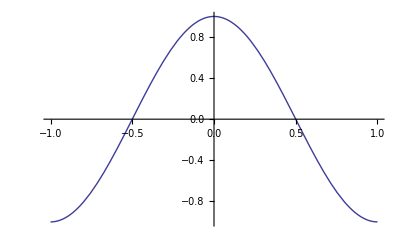

```mathematica
u[x_,t_]:= Cos[π x];
Plot[u[x,t],{x,-1,1},PlotRange->Full]
```

#### Compute degrees of Freedom:

Therefore :

```mathematica
{u^(0),u^(1),u^(2),u^(3),u^(4),u^(5),u^(6)} = Table[ 1/Subscript[Δx, j]^(l+1)∫_Subscript[I, j] (u[x,t] Subscript[v, l])ⅆx,{l,0,6}];
```

```mathematica
{u^(0),u^(1),u^(2),u^(3),u^(4),u^(5),u^(6)} //MatrixForm
```

(0.75
-0.0625
0.
0.0015625
0.
-0.000062004
0.)

#### Solution Approximation u_h

And the approximation of the solution u(x,t) as u_h, is defined as follows

u^h[x,t] = ∑_(l=0)^k a_l u_j^(l)[t]v_l^(j)[x], for x ∈ I_j

here a_l are contants values found to normalize the contribution of each polinomial.

Following the last example we can proceed to compute from the degress of freedom the approximate solution u_h,

```mathematica
NSum[Subscript[a, l] u^(l)Subscript[v, l],{l,0,3}]
```

NSum::nsnum: Summand (or its derivative) a_l\ u^l\ v_l is not numerical at point l = 0.

NSum[a_l u^l v_l,{l,0,3}]

## The Advection Equation

Here we consider numerical solutions of the equations of the hyperbolic conservation laws

∂_t u+∑_(i=1)^d ∂_i f[u]=0

equipped with suitable initial or initial-boundary conditions. Let us examing the RHS:

```mathematica
D[u[x,t], t]+D[f[u[x,t]], x]
```

u^(0,1)[x,t]+f'[u[x,t]] u^(1,0)[x,t]